# Automaty komórkowe

## Wprowadzenie

### Charakteryzacja i definicje

Automaty komórkowe są dyskretnymi modelami rozważanymi między innymi w informatyce, matematyce i fizyce, składającymi się z regularnej siatki o skończonym wymiarze, która składa się z komórek, z których każda może być w jednym z określonych stanów (których pula jest skończona).

Dla każdej z komórek definiuje się zbiór jej sąsiadów jako zbiór komórek położonych w określony sposób względem niej.

Dla automatu komórkowego definiujemy stan początkowy poprzez określenie stanu każdej z komórek. Natomiast nowa generacja komórek powstaje poprzez zastosowanie określonej reguły w postaci funkcji matematycznej, która określa nowy stan każdej z komórek an podstawie stanu komórek w jej sąsiedztwie.

### Trochę historii

Automaty komórkowe zostały odkryte w latach 40-tych przez polskiego matematyka Stanisława Ulama oraz  węgierskiego matematyka Johna von Neumann’a.

Dopiero jednak a latach 70-tych,  kiedy powstała “Gra w życie”, automaty komórkowe opuściły jedynie środowisko akademickie.

W latach 80-tych do grona badaczy nad automatami komórkowymi dołączył Wolfram (twórca Mathematici), który wraz z Matthew Cook’iem dowiódł kompletności Turinga tych automatów.

## Pomocne narzędzia

W celu pracy z automatami komórkowymi zdefiniujemy sobie zestaw pomocnych funkcji, dzięki którym będziemy mogli w bardziej zwięzły i przejrzysty sposób obserwować ewolucję automatów.

```mathematica
AnimateAutomata[rule_, init_,steps_, mapPlot_:ArrayPlot,repetitions_:Infinity]:=
Module[
{automataHistory=CellularAutomaton[rule,init,steps]},
Animate[
mapPlot@automataHistory[[n]],
{n, 1, steps+1, 1},
AnimationRunning->False,
AnimationRepetitions->repetitions
]
];
Print2D=MatrixPlot[#, ColorFunction->"Monochrome",Ticks->None,ImageSize->Tiny, FrameTicks->None]&;
```

## Gra w życie Conway’a

### Opis i zasady

Jest to jeden z pierwszych i bardziej znanych automatów komórkowych, wzbudzający zainteresowanie ze względu na zaskakujący sposób, w jaki potrafią ewoluować struktury na siatce.

Jako sąsiadów komórki w tym automacie definiujemy wszystkie 8 komórek przylegające do danej bokami lub rogami. Każda komórka znajduje się w 1 z 2 stanów - jest “żywa” bądź “martwa”. Komórka martwa rodzi się, wtedy i tylko wtedy gdy ma dokładnie 3 żywych sąsiadów, natomiast komórka żywa pozostaje żywa wtedy i tylko wtedy gdy ma 2 lub 3 żywych sąsiadów, w przypadku innej liczby umiera. W Mathematice regułę tę można zdefiniować w następujący sposób, tak by była prawidłowo interpretowana przez dostępną w Mathematice funkcje CellurarAutomaton

```mathematica
GoLRule=<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->"Moore"|>;
```

Warto zwrócić uwagę, jaki jest sens takiego zapisu tej reguły przejścia automatu komórkowego.

Na początku zależy wyróżnić dwa sposoby ewaluacji generacji komórek: w pierwszej z nich (“TotalisticCode”) bierzemy pod uwagę wszystkie komórki, to jest sąsiedzi + komórka ewoluująca, natomiast w drugiej (“OuterTotalisticCode”) pod uwagę bierzemy oddzielnie sąsiadów komórki i daną komórkę przy zliczaniu liczby żywych komórek. Dla przykładu w przypadku 2D w kodowaniu “TotalisticCode” możemy powiedzieć, że komórka będzie żywa, jeżeli w kwadracie 3x3 w poprzedniej generacji 2 komórki były żywe. Natomiast w kodowaniu “OuterTotalisticCode” możemy powiedzieć, że komórka będzie żywa, jeżeli była żywa i 1 z jej sąsiadów był żywy lub była martwa i 2 jej sąsiadów było żywych.

Warto początkowo zwrócić uwagę, jak wygląda definicja reguł dla jednowymiarowego automatu - definiuje się ją bowiem jako liczbę całkowitą z przedziału [0, 255], a więc liczbę 7 bitową. Jest to związane z tym, że dla automatu jednowymiarowego rozważa się stan środkowej komórki na podstawie stanów jej sąsiadów w określonej kolejności i zapisuje się stany komórek po zmianie w systemie dwójkowym. Dla przykładu sławna “zasada 30” badana przez Wolframa, zapisuje się w systemie binarnym jako

```mathematica
IntegerString[30, 2, 7]
```

0011110

co przekłada się na następujące zasady zmiany przy ewolucji generacji komórek automatu (kolejność przejść jest ustalona w Mathematice)

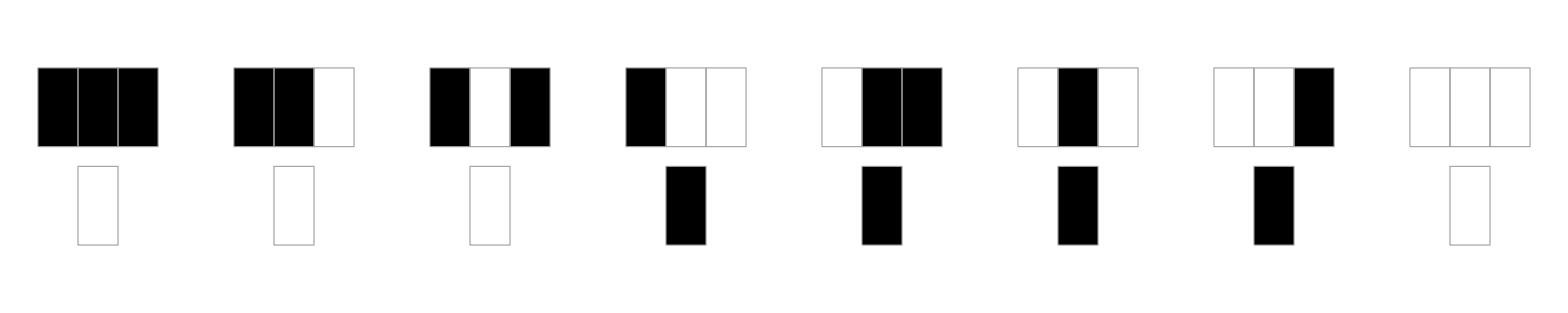

```mathematica
RulePlot@CellularAutomaton[30]
```

Jako że przy generowaniu w Mathematice wszystkich uporządkowanych trójek zer i jedynek dostaniemy wynik właśnie z taką kolejnością, a za pomocą 0 i 1 możemy zdefiniować stan komórki środkowej w następnej generacji.

```mathematica
ArrayPlot[{#},Mesh->All, ImageSize->35]&/@Tuples[{1,0},3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Przypadek dwuwymiarowy jest nieco bardziej skomplikowany, co wynika z tego, że wyróżniamy dla niego co najmniej 2 różne typy sąsiedztwa (które zaprezentujemy za pomocą ilustracji).

```mathematica
GridPlotArray[data_]:= MatrixPlot[SparseArray[data, {5, 5}],Mesh->All,Frame->False];
GridPlotArray/@{{
{i_,j_}/;i==j==3->2, 
{i_,j_}/;EuclideanDistance[{3, 3}, {i, j}]≤√2->1}, 
{{i_,j_}/;i==j==3->3, 
{i_,j_}/;ManhattanDistance[{3, 3},{i,j}]==1->2, 
{i_,j_}/;ManhattanDistance[{3, 3},{i,j}]==2∧EuclideanDistance[{3, 3}, {i, j}]≥2->1}
}//ImageAssemble
```

-Graphics-

Pierwszym z nich jest sąsiedztwo Moore’a, w którym komórka sąsiaduje ze wszystkimi 8 komórkami dookoła siebie. Oprócz tego wyróżniamy również sąsiedztwo von Neumanna, które obejmuje 4 komórki, a w wersji rozszerzonej 8.

Zatem chcąc wyjaśnić znaczenie wyżej zdefiniowanej  zasady gry w życie (GoLRule), potrzebne jest zrozumienie pierwszej jej części - kodu reprezentującego ewaluację komórki do następnej generacji w sąsiedztwie 8 komórek (Moore’a).

```mathematica
IntegerString[224, 2, 18]
```

000000000011100000

Tak więc porównując ten wynik z reprezentacją graficzną zasad “gry w życie” i wiedząc, że komórka w kolejnej generacji jest żywa wtw. gdy miała 3 żywych sąsiadów lub była żywa i miała 2 żywych sąsiadów.

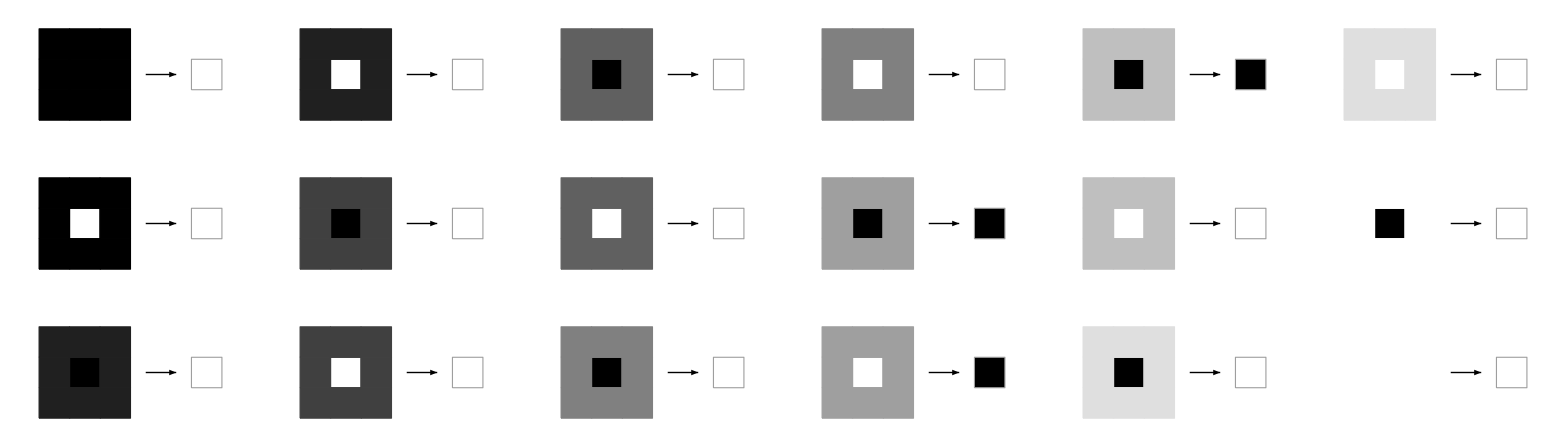

```mathematica
RulePlot[CellularAutomaton[GoLRule]]
```

Widać zatem, że taki zapis zasady ewaluacji komórek za pomocą pojedynczej liczby 18-sto bitowej (jako że stosujemy kodowania “OuterTotalisticRule”) oznacza, dla jakiej liczby sąsiadów komórki komórka środkowa staje się żywa w następnej generacji, gdzie bity liczby odpowiadają kolejnym liczbom żywych sąsiadów komórki (w przypadku sąsiedztwa Moore’a 8, 7, ..., 1, 0, dla kolejno żywej i martwej komórki w poprzedniej generacji).

### Przykłady ewaluacji

Ewolucja automatu komórkowego z przyjęciem zasad gry w życie uwidacznia bardzo ciekawe wzorce. Poniżej zaprezentujemy kilka wybranych, a później przejdziemy do bardziej szczegółowej analizy.

#### Pierwsze starcie:

Ciekawym przykładem na sam początek są takie struktury jak działa, które “produkują” nieustannie ładunki (przykładem jest słynny reprezentant gry “Gosper Glider Gun”)

```mathematica
gosperGliderRun={
{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 1, 1},{0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1},{1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0},{1, 1, 0, 0, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}};
AnimateAutomata[GoLRule,{gosperGliderRun,0},120, Print2D]
```

Poniżej ciekawy przykład, gdzie akcja toczy się w 3-wymiarowym świecie. Wrócimy jeszcze do motywów 3D w tejże prezentacji.

```mathematica
AnimateAutomata[<|"TotalisticCode"->14,"Dimension"->3,"Neighborhood"->27|>,{{{{1}}},0},20, ArrayMesh]
```

## Analiza szczegółowa

### Struktury niezmienne

Przykładami struktur niezmiennych, to jest takich, w których w każdej generacji te same komórki są żywe, są klocek, ul, bochenek, łódź, kadź.

```mathematica
block={{1, 1},{1, 1}};
beehive={{0,1,1,0},{1,0,0,1},{0,1,1,0}};
loaf={{0, 1, 1,0},{1, 0, 0, 1},{0, 1, 0, 1},{0, 0, 1, 0}};
boat={{1, 1, 0},{1, 0, 1},{0, 1, 0}};
tub={{0, 1, 0},{1, 0, 1},{0, 1, 0}};
Column[
AnimateAutomata[GoLRule,{#,0},60, Print2D]&/@{block, beehive, loaf, boat, tub}
]
```

## Oscylatory komórkowe

### Definicja

Na początek spróbujemy skonstruować definicję oscylatora w uniwersum automatu komórkowego Conway’a.

```mathematica
Framed@Text[Style["Niech f: {0,1}^(n^2) -> {0,1}^(n^2) będzie funkcją taką,że f(Plansza_n) = Plansza_(n+1). 
Oscylatorem nazwiemy taki układ planszy, reprezentujący strukturę nie kolidującą z innymi obiektami planszy, że zachodzi
∃_(k ϵ Z) f^k(Plansza_n)= Plansza_(n+k) = Plansza_n  ",TextAlignment->Center]]
```

Niech f: {0,1}^(n^2) -> {0,1}^(n^2) będzie funkcją taką,że f(Plansza_n) = Plansza_(n+1). 
Oscylatorem nazwiemy taki układ planszy, reprezentujący strukturę nie kolidującą z innymi obiektami planszy, że zachodzi
∃_(k ϵ Z) f^k(Plansza_n)= Plansza_(n+k) = Plansza_n

### Przykład oscylatora

#### Wulkan (okres = 5)

```mathematica
fumarole={{0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0},{0,1,1,0,0,1,1,0},{0,1,0,0,0,0,1,0},{0,0,1,0,0,1,0,0},{1,0,1,0,0,1,0,1},{1,1,0,0,0,0,1,1}};
```

```mathematica
AnimateAutomata["GameOfLife",{fumarole,0},10]
```

### Więcej o okresach...

#### Znane okresy

W regułach gry w życie znane są oscylatory o różnych okresach.  W szczególności wiemy, że występują  dowolne struktury o dowolnym okresie poza 19, 38, 41. Nie udowodniono jednak, że takie nie istnieją.

#### Trywialność oscylatora

Oscylator o okresie T jest postrzegany jako nietrywialny, jeśli choć jedna komórka oscyluje z okresem T

#### Stabilność oscylatora

Oscylator o okresie T=1 nazwiemy stabilnym. Jego struktura nigdy się nie zmienia.

#### Częstotliwość występowania

Pomimo iż znane są oscylatory o bardzo dużych okresach (np. 150.000), to najczęściej występującymi są te o okresach 2, 3, 4, 6 lub 8. Odnajdowanie oscylatorów wynika dużej wyobraźni i intuicji przestrzennej,  stąd te najmniejsze są nam znane najbardziej.

#### Konstruowanie oscylatorów

Konstruowanie bazowych oscylatorów, tzn. takich, z których nie da się już wyodrębnić innych jest dosyć skomplikowane. Nie istnieje żaden znany, rozsądny algorytm generujący takie struktury. Jednak posługując się regułami gry w życie (lub innym zestawem reguł dostępnym w uniwersum automatów komórkowych) możemy skonstruować ciąg O_(1,),O_2,..., O_n oscylatorów z okresamy ze zbioru T_1,T_2,..., T_n i umieścić je w takiej odległości od siebie by nie występowała interakcja między nimi. W tej sytuacji mamy oscylator o okresie NWW(T_1,T_2,..., T_n). Przykładowo oscylator o okresie 34 (dla którego przy okazji nie znany jest nietrywialny oscylator) można uzyskać łącząc oscylatory o okresach 2 i 17. Jak można zauważyć, przy tej wiedzy można tworzyć dowolne oscylatory, których okres wynika z najmniejszej wspólnej wielokrotności znanych już oscylatorów.

#### Przykład złożonego oscylatora (okres 34).

```mathematica
period34={{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0},{0,1,1,0,1,0,1,0,1,1,0},{0,1,1,1,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0}};
```

```mathematica
AnimateAutomata["GameOfLife",{period34,0},28]
```

#### Przegląd najbardziej znanych oscylatorów wraz z ich okresami

```mathematica
blinker={{0,0,0},{1,1,1},{0,0,0}};
star={{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,1,1,1,0,1,1,1,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,1,1,0,0},{0,1,1,0,0,0,0,0,0,0,1,1,0},{0,0,1,1,0,0,0,0,0,1,1,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,1,1,1,0,1,1,1,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}};
kiss={{0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,1,0},{0,0,0,0,1,1,0,1,0},{0,0,0,1,0,0,1,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,1,1,0,0,0},{0,0,1,0,0,1,0,0,0},{0,1,0,1,1,0,0,0,0},{0,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0}};
pinwheel={{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,1,0,0,1,0,1,0,0,0},{1,1,0,1,1,0,0,0,1,0,0,0},{0,0,0,1,0,1,0,0,1,0,1,1},{0,0,0,1,0,0,0,0,1,0,1,1},{0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0}};
pulsar={
{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{1, 1, 1, 0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 1},{0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 0},{1, 1, 1, 0, 0, 1, 1, 0, 1, 1, 0, 0, 1, 1, 1},{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0},{0, 0, 0, 0, 1, 1, 0, 0, 0, 1, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0},{0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}};
galaxy={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},{0,0,0,1,1,0,1,1,1,1,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},{0,0,0,1,1,1,1,1,1,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

#### Lista prezentowanych wzorów

```mathematica
desc:={{"oscylator", "okres"},
 {"Migacz", 2},
{"Gwiazda", 3},
{"Francuski Pocałunek", 3},
{"Pulsar", 3},
{"Wiatraczek", 4},
{"Galaktyka", 8}
}
desc //MatrixForm
```

(oscylator | okres
Migacz | 2
Gwiazda | 3
Francuski Pocałunek | 3
Pulsar | 3
Wiatraczek | 4
Galaktyka | 8)

Do wczytywania wzorów z tabali użyjemy zmodyfikowanej funkcji z początku dokumentu:

```mathematica
TableAnimateAutomata[rule_, params_, mapPlot_:ArrayPlot]:=
Module[
{automataHistory=CellularAutomaton[rule,{params[[1]],0},params[[2]]]},
Animate[
mapPlot@automataHistory[[n]],
{n, 1, params[[2]]+1, 1},
AnimationRunning->False,
AnimationRepetitions->Infinity
]
]
```

```mathematica
TableAnimateAutomata["GameOfLife",#1]&/@{
{blinker, 8} ,
{star, 12},
{kiss,12},
{pinwheel, 16},
{pulsar, 12},
{galaxy,32}}
```

{,,,,,}

## Niestałe komórkowe

### Definicja

#### Ścisła

```mathematica
Framed@Text[Style["Niestałą w uniwersum automatów komórkowych nazwiemy taką strukturę Cell["S",ExpressionUUID->"99d4dc23-6f73-402d-bac7-7de00ab0232e"], że nie istnieje Cell["k",ExpressionUUID->"560b5909-8cae-40ab-9ed5-602d6bcb236e"] takie, że f^k(S)= S",TextAlignment->Center]]
```

Niestałą w uniwersum automatów komórkowych nazwiemy taką strukturę Cell["S"], że nie istnieje Cell["k"] takie, że f^k(S)= S

#### Swobodna

Wobec tego niestała jest niczym więcej jak układem, który już nigdy nie powróci do siebie. Zbiór takich układów jest bardzo liczny, w szczególności generując losowe układy komórek, możemy zauważyć, że przytłaczająca większość z nich jest strukturą niestałą. W praktyce bardzo trudno wylosować strukturę, która nie jest niestała.

### Statki

#### Definicja

Aby poruszyć następne definicje, musimy wprowadzić pojęcie statku.

```mathematica
Framed@Text[Style["Statki są okresowymi układamy komórek, które wraz z każdym cyklem przesuwają się o stałą liczbę pół w określonym kierunku",TextAlignment->Center]]
```

Statki są okresowymi układamy komórek, które wraz z każdym cyklem przesuwają się o stałą liczbę pół w określonym kierunku

Statki zawdzięczają swoją nazwę podobieństwu do statków kosmicznych - są to pewne struktury, które w dłuższej perspektywie czasu wyglądają tak samo, jednocześnie przemieszczając się przez przestrzeń uniwersum.

#### Przykład: Lot Dakoty

```mathematica
AnimateAutomata["GameOfLife",{{{0,1,0,0,1},{1,0,0,0,0},{1,0,0,0,1},{1,1,1,1,0}},0},70]
```

#### Przykład: Grider

```mathematica
AnimateAutomata["GameOfLife",{{{0,1,0},{0,0,1},{1,1,1}},0},70]
```

### Stabilizacja

#### Definicja

```mathematica
Framed@Text[Style["Stabilizacją nazywamy przejście układu do zestawu układów stabilnych, oscylatorów i statków",TextAlignment->Center]]
```

Stabilizacją nazywamy przejście układu do zestawu układów stabilnych, oscylatorów i statków

#### Współczynnik stabilizacji (L)

```mathematica
Framed@Text[Style["Współczynnikiem stabilizacji nazwiemy stosunek liczby kroków potrzebnych w celu stabilizacji, do początkowej liczby żywych komórek",TextAlignment->Center]]
```

Współczynnikiem stabilizacji nazwiemy stosunek liczby kroków potrzebnych w celu stabilizacji, do początkowej liczby żywych komórek

Wobec tego stabilizacja, to swojego rodzaju przejście z chaotycznego stanu do ustabilizowanego, zaś współczynnik stabilizacji mówi nam, jak bardzo trudny do ustabilizowania był układ, biorąc pod uwagę początkową liczbę komórek żywych, które należało okiełznać.  Jest to o tyle ciekawe zjawisko, bowiem czytelnik mógłby dojść do wniosku, że plansze albo mają skłonność do relatywnie szybkiej stabilizacji (niski współczynnik stabilizacji), albo pozostanie w chaosie do końca. Jednakże niektóre struktury mają  bardzo wysoki współczynnik stabilizacji.

#### R-pentomino: Przykład układu z wysokim współczynnikiem stabilizacji (L=221)

```mathematica
AnimateAutomata["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},1200]
```

#### Matuzalema

Aby sformalizować układy z wysokim L, wprowadzono następującą definicję.

```mathematica
Framed@Text[Style["Matuzalemem nazwiemy układ z wysokim współczynnikiem stabilizacji.",TextAlignment->Center]]
```

Matuzalemem nazwiemy układ z wysokim współczynnikiem stabilizacji.

R-pentomino z poprzedniego przykładu jest przykładem Matuzalema. Innym znanym Matuzalemem ze współczynnikiem L=700 jest tzw. żołądź. Stabilizuje się on po ok. 5300 krokach. Ze względu na ograniczenia RAM zostanie pokazane jego pierwsze 1000 kroków.

```mathematica
AnimateAutomata["GameOfLife",{{{0,1,0,0,0,0,0}, {0,0,0,1,0,0,0}, {1,1,0,0,1,1,1}},0},1000]
```

### Die-Hardy

#### Definicja

```mathematica
Framed@Text[Style["DieHardem nazwiemy układ, który umiera po skończonym czasie Cell["T",ExpressionUUID->"81d8f737-5b6e-4200-90d6-7e2ef214fc61"], jednak Cell["T",ExpressionUUID->"42c2f820-8b07-41af-a84f-9919087c0c09"] jest postrzegany jako duży.",TextAlignment->Center]]
```

DieHardem nazwiemy układ, który umiera po skończonym czasie Cell["T"], jednak Cell["T"] jest postrzegany jako duży.

Jak widzimy, powyższa definicja nie jest do końca ścisła, ponieważ nikt nie sprecyzował, jak duży czas umierania musi być. Nie mniej jednak wśród zbioru wszystkich umierających po skończonym czasie układów, jesteśmy w stanie wskazać te, których T znacząco przewyższa inne.

#### Przykład

```mathematica
AnimateAutomata["GameOfLife",{{{0,0,0,0,0,0,1, 0}, {1,1,0,0,0,0,0, 0}, {0,1,0,0,0,1,1, 1}},0},150]
```

### Ogrody Edenu

#### Definicja

```mathematica
Framed@Text[Style["Ogrodem Edenu nazwiemy taki układ Cell["S",ExpressionUUID->"2cb40eed-d812-4a57-933e-0f8768adea6e"], dla którego nie istnieje stan początkowy S_0 oraz następujące po nim S_1, S_2,..., S_k takie, że S_k=S.",TextAlignment->Center]]
```

Ogrodem Edenu nazwiemy taki układ Cell["S"], dla którego nie istnieje stan początkowy S_0 oraz następujące po nim S_1, S_2,..., S_k takie, że S_k=S.

Innymi słowy, Ogrody Edenu to takie układy, nie mogły powstać jako ciąg przekształceń pewnego układu S_0. Mogą one być zatem tylko i wyłącznie układami początkowymi w symulacji.

#### Przykład

Poniżej znajduje się jeden z najmniejszych znanych przykładów Ogrodów Edenu. Proszę, abyśmy zwrócili uwagę na ich rozmiar - mimo wszystko jest imponująco duży.

```mathematica
AnimateAutomata["GameOfLife",{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,0,0,0,0,0,0,0},{0,1,1,0,1,0,1,1,1,1,1,0,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,0},{0,0,1,1,1,1,0,1,0,1,1,1,0,0,0},{0,1,0,1,0,1,1,0,1,1,1,0,1,0,0},{0,0,1,1,1,0,1,1,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,1,1,1,0,0,1,1,0},{0,0,1,0,1,1,0,1,0,1,0,1,1,0,0},{0,1,1,1,0,1,1,1,1,0,1,0,1,0,0},{0,0,1,0,1,1,1,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,1,0,0,1,0,0,0,0},{0,0,1,1,0,1,0,0,1,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},0},25]
```

#### Algorytm

Ogrody Edenu są na tyle ciekawym zjawiskiem w uniwersum Conway’a, że doczekały się wielu badań na ich temat. Istnieje algorytm liniowego wykrywania ogrodów edenu w czasie wielomianowym.

```mathematica
Framed@Text[Style["An Efficient Algorithm for the Detection of Eden (David J. Warne, Ross F. Hayward, Neil A. Kelson, Dann G. Mallet)",TextAlignment->Center]]
```

An Efficient Algorithm for the Detection of Eden (David J. Warne, Ross F. Hayward, Neil A. Kelson, Dann G. Mallet)

Sam algorytm jest skomplikowany i wielofazowy. Jednak sukcesem jest to, że w ogóle takowy istnieje, gdyż dla  d>1 wymiarów udowodniono, że nie istnieje taki algorytm, który gwarantuje skończenie i danie poprawnej odpowiedzi. Dowód ten sformułował fiński matematyk i informatyk Jarkko Kari w swojej pracy:

```mathematica
Framed@Text[Style["Reversibility of 2D cellular automata is undecidable (Jarkko Kari)",TextAlignment->Center]]
```

Reversibility of 2D cellular automata is undecidable (Jarkko Kari)

#### Twierdzenie o Ogrodach Edenu

Na początek wprowadzimy definicję Bliźniaka.

```mathematica
Framed@Text[Style["W automacie komórkowym dwa skończone wzory są bliźniakami, jeśli jeden można zastąpić drugim, gdziekolwiek się pojawi, bez zmiany przyszłych konfiguracji. ",TextAlignment->Center]]
```

W automacie komórkowym dwa skończone wzory są bliźniakami, jeśli jeden można zastąpić drugim, gdziekolwiek się pojawi, bez zmiany przyszłych konfiguracji.

Teraz możemy sformułować twierdzenie o ogrodach edenu:

```mathematica
Framed@Text[Style["Automat komórkowy posiada Ogród Edenu wtedy i tylko wtedy gdy posiadania konstrukcje bliźniaków.",TextAlignment->Center]]
```

Automat komórkowy posiada Ogród Edenu wtedy i tylko wtedy gdy posiadania konstrukcje bliźniaków.

Jest to bardzo ciekawa równoważność. Sprawdzenie, czy dwa wzory są bliźniakami, jest łatwo obliczalne. Problemem natomiast jest znajdowanie takich bliźniaków, stąd twierdzenie to posłuży nam dzisiaj raczej jako ciekawostkę, niżeli jako konkretne narzędzie.

## Modyfikacje Reguł

# Wstęp

#### Mały powrót...

Widziane przez nas wcześniej symulacje dotyczyły głównie tradycyjnych reguł gry w życie, dokładnie tych, które zostały opracowane przez ich twórcę: Johna Conwaya. Jednakże warto również pochylić się nad najróżniejszymi regułami.

#### Co właściwie możemy modyfikować?

Zastanówmy się jeszcze raz, co właściwie determinuje zachowanie komórek na planszy? Po pierwsze to, że akcja dzieje się w pewnym uniwersum pewnych stanów, które dla danego kroku możemy zapisać jako funkcje Z x Z → {0,1}, tudzież jego podzbiorze. Nie musimy brnąć dalej by już na tym etapie mieć szerokie pole do popisu. Możemy po pierwsze zmieniać wymiarowość naszej przestrzeni, na przykład co się stanie, jeśli poprzez analogię przeniesiemy nasze reguły do uniwersum k wymiarowego? A co się stanie, gdy zbiór możliwych stanóœ nie będzie binarny? Wobec tego rozważania możemy uogólnić na Z^k→ {0,1,...,n-1,n} dla pewnych k, n.

#### Czy to wszystko...? Słów kilka o sąsiadach

Otóż nie! Automaty wówczas nie byłyby tak ciekawe. Brnąc dalej, przypomijny z początku naszej opowieści, że mamy dwie możliwości sąsiedztwa: Moore’a oraz von Neumanna. Tutaj zaimplementowana jest możliwość poeksperymentowania z tymi sąsiedztwami. Na panelu kontrolnym możemy modyfikować promień działania sąsiedztwa.

```mathematica
MooreNeighborhood[r_,m_]:=Table[If[Abs[x]≤r&&Abs[y]≤r,1,0],{x,-m,m},{y,-m,m}]
vonNeumannNeighborhood[r_,m_]:=Table[If[Abs[x]+Abs[y]≤r,1,0],{x,-m,m},{y,-m,m}]
```

```mathematica
Manipulate[ArrayPlot[mvn[r,r+1],Mesh->True],
{{mvn,MooreNeighborhood,"neighborhood"},
{MooreNeighborhood->"Moore",vonNeumannNeighborhood->"VonNeumann"},
ControlType->SetterBar},
{{r,1,"range"},1,14,1,
Appearance->"Labeled"}]
```

Sąsiedztwo Moore’a polega na tym, że za sąsiadów każdej komórki, uważamy  wszystkie stykające się z nią co najmniej jednym rogiem (8 sąsiadów).
Sąsiedztwo von Neumanna  polega na tym, że za sąsiadów uważamy tylko te, które mają wspólną krawędź z interesującą nas komórką (4 sąsiadów).

W klasycznej grze w życie uznajemy sąsiedztwo Moore’a z parametrem r=1.

#### Mówiąc reguły mamy na myśli...

Wielokrotnie w tejże pracy poruszaliśmy pojęcie reguł. Za każdym razem mając na myśli ciągi warunków zależnych od:

Stanu rozważanej komórki (klasycznie 0/1)

Liczby żywych sąsiadów

Liczby martwych sąsiadów

Zależnie od tych parametrów komórka najczęściej umierała z samotności, umierała z zatłoczenia lub rodziła się.

#### Notacja dla reguł

Reguły ze względu na mnogość swoją notację mieć muszą. Występuje kilka ciekawych notacji, jednakże my posłużymy się notacją By/Sx

```mathematica
Framed@Text[Style["Notacja By/Sx, używana powszechnie w najpopularniejszych programie open-source do symulacji automatów komórkowych, Golly, jest zapisywana w formie By/Sx gdzie B oznacza Birth, S oznacza survival, x oraz y są ciągami liczb od 0 do 8. Obecność cyfry d w ciągu x oznacza, że żywa komórka z d żywymi sąsiadami przeżywa do następnej generacji, a obecność d w ciągu y oznacza, że żywa komórka z d żywymi sąsiadami przeżywa do następnej generacji.",TextAlignment->Center]]
```

Notacja By/Sx, używana powszechnie w najpopularniejszych programie open-source do symulacji automatów komórkowych, Golly, jest zapisywana w formie By/Sx gdzie B oznacza Birth, S oznacza survival, x oraz y są ciągami liczb od 0 do 8. Obecność cyfry d w ciągu x oznacza, że żywa komórka z d żywymi sąsiadami przeżywa do następnej generacji, a obecność d w ciągu y oznacza, że żywa komórka z d żywymi sąsiadami przeżywa do następnej generacji.

W Mathematice tę notację możemy używać przy pomocy GrowthSurvivalCases: (https://reference.wolfram.com/language/ref/CellularAutomaton.html)

## Nieco prezentacji

#### Klasyczna gra w życie z sąsiedztwem von Neumanna

Nieco wcześniej pokazywaliśmy strukturę, która przypominała lot ptaka. Zobaczmy, co się stanie, gdy zmienimy styl sąsiedztwa.

```mathematica
GoLRule=<|"OuterTotalisticCode"->224,"Dimension"->2,"Neighborhood"->"VonNeumann"|>;
AnimateAutomata[GoLRule,{{{0,1,0,0,1},{1,0,0,0,0},{1,0,0,0,1},{1,1,1,1,0}},0},5]
```

Jak widać, ptak od razu zanika. Wszakże nie zawsze tak jest. Istnieją bowiem układy, dla których otrzymujemy zupełnie inne, ciekawe zachowania planszy. Poniżej znajduje się przywołany przez nas wcześniej ogród edenu, który w tym sąsiedztwie przekształca się w stałe kwadraty.

```mathematica
AnimateAutomata[GoLRule,{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,0,0,0,0,0,0,0},{0,1,1,0,1,0,1,1,1,1,1,0,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,0},{0,0,1,1,1,1,0,1,0,1,1,1,0,0,0},{0,1,0,1,0,1,1,0,1,1,1,0,1,0,0},{0,0,1,1,1,0,1,1,0,1,0,1,0,0,0},{0,0,0,1,0,0,0,1,1,1,0,0,1,1,0},{0,0,1,0,1,1,0,1,0,1,0,1,1,0,0},{0,1,1,1,0,1,1,1,1,0,1,0,1,0,0},{0,0,1,0,1,1,1,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,1,0,0,1,0,0,0,0},{0,0,1,1,0,1,0,0,1,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},0},25]
```

### Sąsiedztwo Moore’a ale... reguły nieklasyczne

#### Niech stanie się chaos! Czyli ziarenka...

Reguła B2/S charakteryzuje się intensywnym wybuchem komórek. Reguły te zwane są ziarenkami.

```mathematica
NRule=<|"GrowthSurvivalCases"->{{2},{}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0,0,1},{1,0,0,0,0},{1,0,0,0,1},{1,1,1,1,0}},0},100]
```

#### High Life - czyli lustrzana siostra Game Of Life

Ma nieco inne reguły, lecz charakteryzuje się podobnymi efektami, co oryginalny zamysł. Zapis: B36/S23

```mathematica
NRule=<|"GrowthSurvivalCases"->{{3,6},{2,3}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0,0,0,0,0}, {0,0,0,1,0,0,0}, {1,1,0,0,1,1,1}},0},600]
```

#### Nieco pozytywniej... Life Without Death

Bardzo pozytywna wersja automatu komórkowego. W tym modelu komórka nigdy nie umiera. Za to następują ciekawe wzory rozrostu. Zapis: B3/S012345678

```mathematica
NRule=<|"GrowthSurvivalCases"->{{3},{0,1,2,3,4,5,6,7,8}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0,0,0,0,0}, {0,0,0,1,0,0,0}, {1,1,0,0,1,1,1}},0},600]
```

```mathematica
NRule=<|"GrowthSurvivalCases"->{{3},{0,1,2,3,4,5,6,7,8}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0}, {0,1,1},{1,0,1}},0},600]
```

Choć okazuje się, że nasza pozytywna wersja też potrafi mieć stabilniejsze momenty. Oto jedna z form się stabilizujących:

```mathematica
NRule=<|"GrowthSurvivalCases"->{{3},{0,1,2,3,4,5,6,7,8}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{1,0,1}, {0,1,0},{1,0,1}},0},15]
```

#### Betonowe Dżungle... miasta

Cóż... tworzymy miasta... ale nie byle jakie! W środku tętni życie a my je otaczamy murem!

```mathematica
NRule=<|"GrowthSurvivalCases"->{{4,5,6,7,8},{2,3,4,5}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0,0,1},{1,0,0,0,0},{1,0,0,0,1},{1,1,1,1,0}},0},15]
```

```mathematica
NRule=<|"GrowthSurvivalCases"->{{4,5,6,7,8},{2,3,4,5}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,1,1,0,0,0,0,0,0,0},{0,1,1,0,1,0,1,1,1,1,1,0,1,0,0},{0,1,0,1,0,1,1,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,1,1,0,1,1,1,0,1,0,0},{0,0,1,0,1,0,1,1,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,1,0,0,1,1,0},{0,0,1,0,1,1,0,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,1,0,1,1,1,1,0,0,0,1,0,0,0},{0,0,1,0,1,0,1,1,0,0,1,0,0,0,0},{0,0,1,1,0,1,0,0,1,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},0},30]
```

#### Replikator w akcji

Jedną z najbardziej interesujących reguł jest replikator. Charakteryzuje się tym, że po pewnej ustalonej liczbie kroków odtwarza on rzeczy ukazane na starcie.

```mathematica
NRule=<|"GrowthSurvivalCases"->{{1,3,5,7},{1,3,5,7}},"Dimension"->2|>;
AnimateAutomata[NRule,{{{0,1,0,1,0,1,0}, {0,0,0,1,0,0,0}, {0,1,1,1,1,1,0}},0},50]
```

### Oraz na koniec

```mathematica
NRule=<|"GrowthSurvivalCases"->{{1,3,5,7},{1,3,5,7}},"Dimension"->2|>;
data = {{{0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,0,0},{0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,1,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,1,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0,0}}
,0};
MimuwWita [k_]:= AnimateAutomata[NRule,data,k,ArrayPlot, 1 ]
MimuwWita[64]
```

Nade wszystko fascynującym jest, że w pewnych momentach może nam się wydawać, że mamy do czynienia z pewnym szumem, nie niosącym żadnych informacji. Otóż nic bardziej mylnego. Okazuje się, że podczas swojego żywota, wzorzec replikatora nieustannie niesie w sobie informacje wystarczające do odtworzenia konstrukcji, która została mu powierzona na samym początku. Czasami, jak między innymi widać na powyższych przykładach, kopie początkowego układu zaczynają ze sobą kolidować. To może pozornie stwarzać wrażenie problemu, ponieważ nachodzące na siebie konstrukcje mogłyby wytrącić cały układ z równowagi. Jednak właśnie cała istota replikatora, polega na przekształcaniu obrazu bazowego, stopniowo w pewien szum, z którego wyłaniają się następne kopie.

Poniżej pokażemy jeszcze, że kontynuacja procesu replikowania pozwala wytwarzać coraz więcej i więcej oryginalnych obrazków. Choć należy zauważyć, że proces nie jest monotoniczny, poniżej widzimy, że kończy się na 24 napisach...

```mathematica
MimuwWita[192]
```

...żeby po 256 krokach znów powrócić do 8 napisów. Wszakże są one dalej od siebie oddalone więc z czasem rośnie potencjał na większe ilości napisów pomiędzy cyklami.

```mathematica
MimuwWita[256]
```

#### Własna implementacja automatów komórkowych

W ramach pracy nad automatami komórkowymi stworzyliśmy funkcję umożliwiającą użytkownikowi na bardziej skomplikowane ewolucje generacji, niż jest to w przypadku standardowych funkcji Mathematici. Stworzona funkcja została zaimplementowana dla przypadku trójwymiarowego, dla którego efekty końcowy jest najbardziej efektowny. Umożliwia ona tworzenie generacji, których życie przebiega w bardziej ciągły sposób, to znaczy nie mówimy jedynie o komórkach żywych i martwych, ale o etapie życia komórek z przedziału [0, 1]. Ponadto umożliwia ona uwzględnienie pozycji absolutnej danej komórki w świecie i w ten sposób wpływanie na jej dalsze życie.

```mathematica
(* Dodawanie 9 kopii generacji dookoła niej *)
AddSurrounding[matrix_]:=
Module[{j1, j2, j3},
j1=Join[matrix, matrix, matrix];
j2=Join[j1, j1, j1, 2];
j3=Join[j2, j2, j2, 3];
j3];

(* Wycinanie sąsiedztwa zadanej komórki w macierzy       *)
(* Zgodnie z konwencją Mathemtici numerujemy pozycje od 1 *)
(* Funkcja w przypadku 3D zwracaotoczenie komórki to jest *)
(* 27 komórek z aktualnej generacji                       *)
Neighbourhood[matrix_, position_,dimen_,distance_:1]:=
Module[{
x=dimen[[1]]+position[[1]], 
y=dimen[[2]]+position[[2]], 
z=dimen[[3]]+position[[3]]}, 
matrix[[
x-distance;;x+distance,
y-distance;;y+distance, 
z-distance;;z+distance]]
];

(* Ewaluacja pojedynczej generacji na podstawie macierzy poprzedniej *)
ProduceNextGeneration[matrix_, rule_]:=
Module[{
x=Dimensions[matrix][[1]], 
y=Dimensions[matrix][[2]], 
z=Dimensions[matrix][[3]],
surrMatrix=AddSurrounding[matrix]
},
Table[rule[Neighbourhood[surrMatrix, {i, j, k},{x, y, z}],i,j,k],
{i, 1,x},{j, 1, y},{k, 1,z}]
];

CellularFunctionalAutomaton[rule_, init_,steps_]:=
Module[{
history={init}
},{
For[i=1, i≤ steps, i++, 
AppendTo[history, ProduceNextGeneration[Last@history, rule]]
];
history
}];

AnimateFunctionalAutomata[rule_, init_,steps_]:=
Module[
{automataHistory=CellularFunctionalAutomaton[rule,init,steps]},
Animate[
ArrayMesh[automataHistory[[1]][[n]],
MeshCellStyle->MapIndexed[{3,First[#2]}->GrayLevel[1-#1]&,Select[Flatten@automataHistory[[1]][[n]], #≠0&]]],
{n, 1, steps+1, 1},
AnimationRunning->False,
AnimationRepetitions->Infinity
]
];

(* Losowo wymyślona zasada ewaluacji generacji komórek *)
RandomRule[neigh_, i_, j_, k_]:=
Module[{count, center},
count=Total[neigh,Infinity];
center=neigh[[2]][[2]][[2]];
If[Or[
And[count > 4, count < 15, center>0], 
And[count > 3, count < 13, center==0]], center+(count/27), 0]
];

Gravity[neigh_, i_,j_,k_]:=
Module[{top},
top=neigh[[2]][[1]][[2]];
If[j!=20,top,0]
];

GravityFadeout[neigh_, i_,j_,k_]:=
Module[{top},
top=neigh[[2]][[1]][[2]];
If[j!=20,If[top≥0.1, top-0.1, top],0]
];
```

```mathematica
cross=Table[If[i==j==k ||i==21-k==j||i==21-j==k||21-i==j==k,1,0],{i,20},{j,20},{k,20}];
```

```mathematica
AnimateFunctionalAutomata[RandomRule, cross, 50]
```

```mathematica
AnimateFunctionalAutomata[Gravity, cross, 19]
```

```mathematica
AnimateFunctionalAutomata[GravityFadeout, cross, 19]
```

## Podsumowanie

W stworzonej przez nas pracy staraliśmy się w jak najbardziej ścisły, a zarazem jasny sposób zdefiniować i opisać działanie automatów komórkowych. Naszym zdaniem są one bardzo ciekawym bytem matematycznym, którego Mathematica ułatwia eksplorację w niezwykły sposób, poprzez możliwość szybkiego tworzenia nowych modeli i prób ich ewaluacji. Zaprezentowane przez nas przykłady pokazują, jak różnorodne może być zachowanie się kolejnych generacji w automatach komórkowych oraz jak różne czynniki wpływają na dalszy rozwój generacji. Mamy nadzieję, iż osoby zapoznające się z naszą pracą, dzięki jej charakterowi, również mogły zachwycić się działaniem automatów komórkowych i poznać wiele do tej pory niespotkanych i interesujących zjawisk matematycznych.

Michał Tyrolski, Maciej Procyk